```mathematica
Map[{a,b,c,d}/.#&,Solve[{a/2+b/4+c/8+d/16==1,a≥0,b≥0,c≥0,d≥0},Integers]]//Length
```

35

```mathematica
Monitor[Table[Length[Table[Subscript[a, i],{i,1,mm}]/.Solve[Join[{Sum[Subscript[a, i]/2^i,{i,1,mm}]==1},Table[Subscript[a, i]≥0,{i,1,mm}]],Integers]],{mm,1,7}],mm]
```

{1,3,9,35,201,1827,27337}

Rectangle[{0,0}]

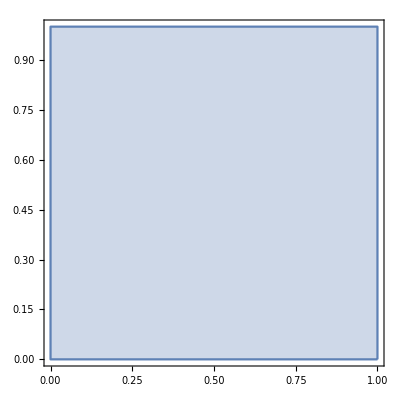
{-Graphics-,Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]}

```mathematica
Rectangle[]
{RegionPlot[%],RegionBoundary[%]}
```

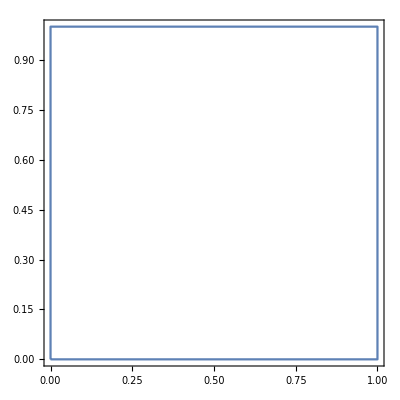

```mathematica
RegionPlot[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]]
```

{{{0,0},{1,0}},{{1,0},{1,1}},{{1,1},{0,1}},{{0,1},{0,0}}}

RegionMeasure::reg: RegionIntersection[Line[{{1, 2}, {2, 3}}], Line[{{3/2, 5/2}, {5/2, 3/2}}]] is not a correctly specified region.

RegionCentroid::reg: RegionIntersection[Line[{{1, 2}, {2, 3}}], Line[{{3/2, 5/2}, {5/2, 3/2}}]] is not a correctly specified region.

RegionMeasure::reg: RegionIntersection[Line[{{1, 2}, {2, 3}}], Line[{{3/2, 5/2}, {5/2, 3/2}}]] is not a correctly specified region.

RegionMeasure::reg: RegionIntersection[Line[{{3/2, 5/2}, {5/2, 3/2}}], Line[{{4, 1}, {1, 2}}]] is not a correctly specified region.

General::stop: Further output of RegionMeasure :: reg will be suppressed during this calculation.

RegionCentroid::reg: RegionIntersection[Line[{{3/2, 5/2}, {5/2, 3/2}}], Line[{{4, 1}, {1, 2}}]] is not a correctly specified region.

{{{2,3},{3,4}},{{3,4},{4,1}},{{1,2},{3/2,5/2}},{{3/2,5/2},{2,3}},{{4,1},{5/2,3/2}},{{5/2,3/2},{1,2}},{{3/2,5/2},{5/2,3/2}}}

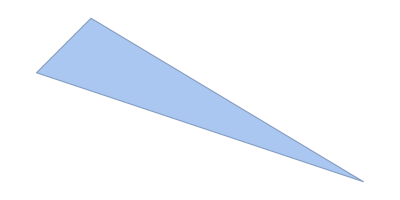
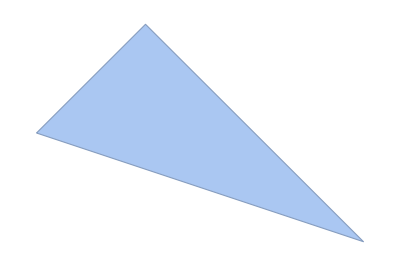
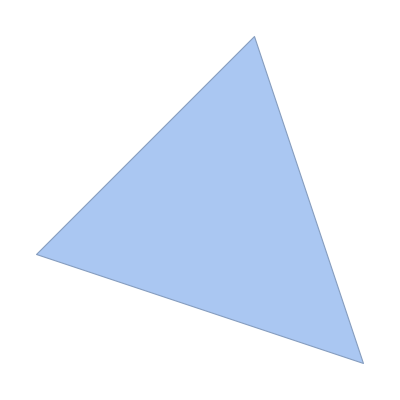
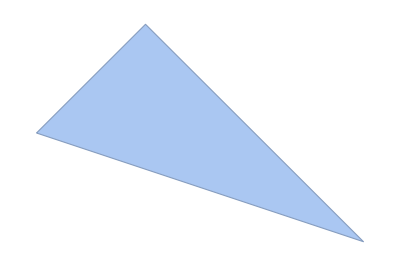
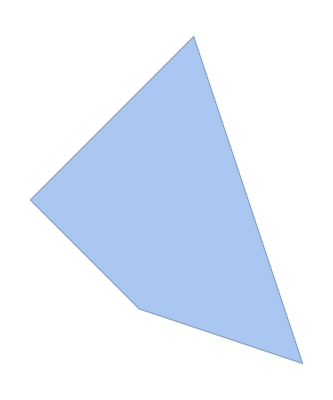
{1.,{{{1,2},{2,3}},{{2,3},{3,4}},{{3,4},{4,1}},{{4,1},{1,2}}},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{{1.},{1.,0.5},{1.33333,1.,1.},{1.,1.,1.33333,1.},{1.33333,1.,1.,1.33333,1.},{2.,2.,2.,2.,2.,2.},{4.,4.,4.,4.,4.,4.,3.5},{4.,4.,4.,4.,4.,4.,4.,4.},{4.,4.,4.,4.,4.,4.,4.,4.,4.},{4.,4.,4.,4.,4.,4.,4.,4.,4.,4.},{4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.},{4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.},{4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.}},{-Graphics-,-Graphics-}}

```mathematica
someedges={{{0,0},{1,0}},{{1,0},{1,1}},{{1,1},{0,1}},{{0,1},{0,0}}}
splitregion[region_,{midpt1_,midpt2_},previousmidpoints_]:=
Block[{area=RegionMeasure[region],edges=region2linelist[region]},
Block[{midpoints=Join[Map[(#[[1]]+#[[2]])/2&,edges],previousmidpoints]},
Block[{newedge={midpoints[[midpt1]],midpoints[[midpt2]]}},
Block[{newedges=Join[Complement[edges,Select[edges,lineinterq[newedge,#]&]],Flatten[Map[Block[{thisinter=lineinter[newedge,#]},{{#[[1]],thisinter},{thisinter,#[[2]]}}]&,Select[edges,lineinterq[newedge,#]&]],1],{newedge}]},Print[newedges];
Block[{subregions=Map[ConvexHullMesh[DeleteDuplicates[Flatten[Map[newedges[[#]]&,#],1]]]&,DeleteDuplicates[Map[DeleteDuplicates,ToExpression[StringReplace[ToString[FindCycle[Graph[edges2graph[newedges]],(*5*)Infinity,All]],{"<->"->","}]]]]]},
Block[{chosensubregions=Position[Table[Table[RegionMeasure[RegionUnion[subregions[[i]],subregions[[j]]],2],{i,1,j}],{j,1,Length[subregions]}],area]},
{(*newedges,subregions,*)area,edges,subregions,Table[Table[RegionMeasure[RegionUnion[subregions[[i]],subregions[[j]]],2],{i,1,j}],{j,1,Length[subregions]}],{subregions[[(chosensubregions[[1,1]])]],subregions[[(chosensubregions[[1,2]])]]}}]]]]]]
RegionPlot[DiscretizeGraphics[Rectangle[]]];
splitregion[DiscretizeGraphics[Rectangle[]],{1,4},{}]
```

```mathematica
RandomChoice[{"y","n"}]
```

y

```mathematica
Position[{{1.},{3.1999999999999993,3.},{3.,4.,2.5},{2.,3.,4.,1.5},{4.,4.,4.,4.,4.},{3.,4.,3.,4.,4.,3.},{2.,3.1999999999999993,4.,2.,4.,4.,2.},{3.1999999999999993,3.,4.,3.,4.,4.,3.1999999999999993,3.},{4.,4.,4.,4.,4.,4.,4.,4.,4.},{4.,4.,4.,4.,4.,4.,4.,4.,4.,4.},{4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.},{4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.},{4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.}},1.]
```

{{1,1}}

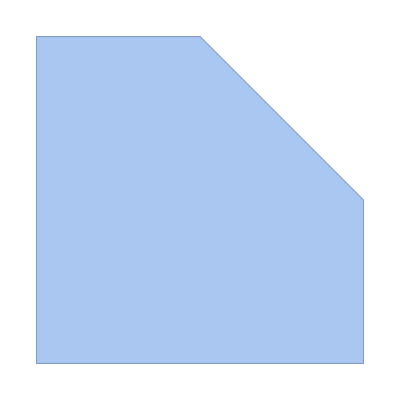
```mathematica
splitregion[-Graphics-,{2,3},{}]
```

RegionMeasure::reg: RegionIntersection[Line[{{4, 5}, {5, 3}}], Line[{{9/2, 4}, {4, 5/2}}]] is not a correctly specified region.

RegionCentroid::reg: RegionIntersection[Line[{{4, 5}, {5, 3}}], Line[{{9/2, 4}, {4, 5/2}}]] is not a correctly specified region.

RegionMeasure::reg: RegionIntersection[Line[{{4, 5}, {5, 3}}], Line[{{9/2, 4}, {4, 5/2}}]] is not a correctly specified region.

RegionMeasure::reg: RegionIntersection[Line[{{9/2, 4}, {4, 5/2}}], Line[{{5, 3}, {3, 2}}]] is not a correctly specified region.

General::stop: Further output of RegionMeasure :: reg will be suppressed during this calculation.

RegionCentroid::reg: RegionIntersection[Line[{{9/2, 4}, {4, 5/2}}], Line[{{5, 3}, {3, 2}}]] is not a correctly specified region.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {} ⟦ 1, 1 ⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {} ⟦ 1, 2 ⟧ cannot be used as a part specification.

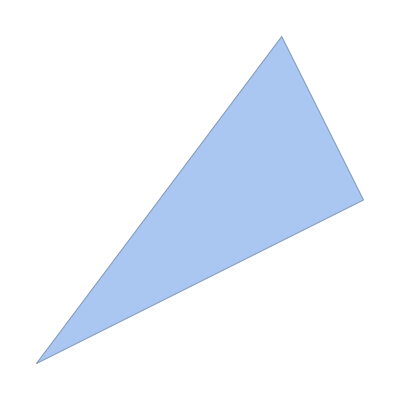
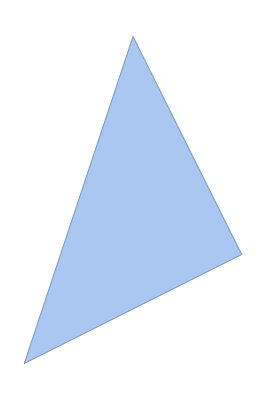
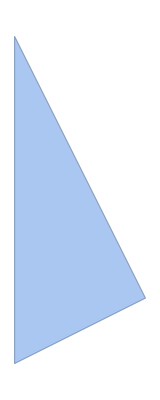
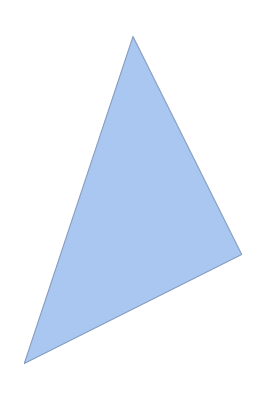
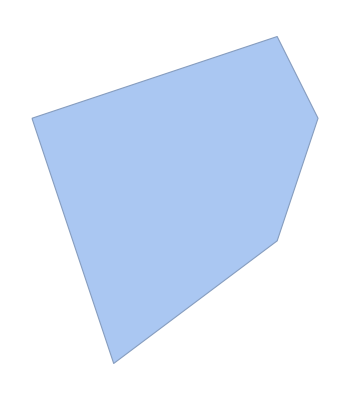
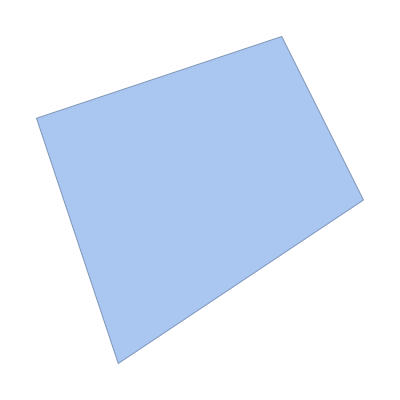
{0.875,{{1.25},{1.25,0.625},{1.66667,1.25,1.25},{1.25,1.25,1.66667,1.25},{1.66667,1.25,1.25,1.66667,1.25},{2.5,2.5,2.5,2.5,2.5,2.5},{8.75,8.75,8.75,8.75,8.75,8.75,8.125},{9.,9.,9.,9.,9.,9.,9.,9.},{9.,9.,9.,9.,9.,9.,9.,9.,9.},{9.,9.,9.,9.,9.,9.,9.,9.,9.,9.},{9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.},{9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.},{9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦{}⟦1,1⟧⟧,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦{}⟦1,2⟧⟧}}

```mathematica
Position[{{1.25},{1.25,0.625},{1.666666666666666,1.25,1.25},{1.25,1.25,1.666666666666666,1.25},{1.666666666666666,1.25,1.25,1.666666666666666,1.25},{2.5,2.5,2.5,2.5,2.5,2.5},{8.75,8.75,8.75,8.75,8.75,8.75,8.125},{9.,9.,9.,9.,9.,9.,9.,9.},{9.,9.,9.,9.,9.,9.,9.,9.,9.},{9.,9.,9.,9.,9.,9.,9.,9.,9.,9.},{9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.},{9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.},{9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.}},0.875]
```

{}

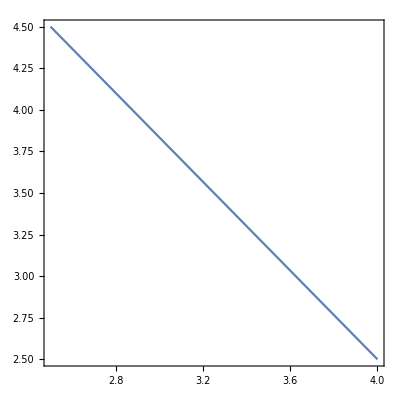
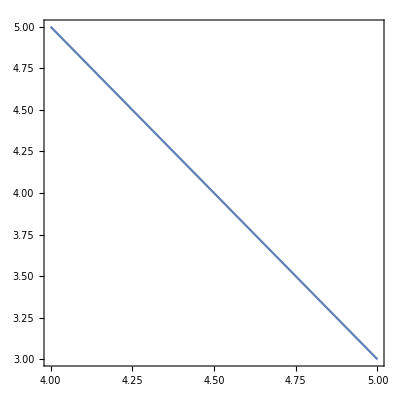

```mathematica
Map[RegionPlot,{Line[{{5/2,9/2},{4,5/2}}],Line[{{4,5},{5,3}}]}]
```

```mathematica
MeshCells[DiscretizeGraphics[Rectangle[]],1]
```

{Line[{1,2}],Line[{2,3}],Line[{3,4}],Line[{4,1}]}

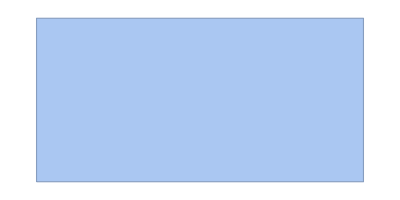
```mathematica
Map[#[[1]]&,MeshCells[-Graphics-,1]]
region2linelist[inregion_]:=Block[{lines=Map[#[[1]]&,MeshCells[inregion,1]]},Table[{lines[[1+Mod[i-1,Length[lines]]]],lines[[1+Mod[i,Length[lines]]]]},{i,1,Length[lines]}]]
region2linelist[-Graphics-]
```

{{1,3},{3,4},{4,2},{2,1}}

{{{1,3},{3,4}},{{3,4},{4,2}},{{4,2},{2,1}},{{2,1},{1,3}}}

```mathematica
RegionPlot[[Polygon[{{0,0},{1,0},{1,1},{0,1},{0,0}}]]]
```

RegionPlot::invplotreg: {MeshRegion[Polygon[{{0, 0}, {1, 0}, {1, 1}, {0, 1}, {0, 0}}]]} is not a valid region to plot.

RegionPlot[MeshRegion[Polygon[{{0,0},{1,0},{1,1},{0,1},{0,0}}]]]

```mathematica
MeshCells[DiscretizeGraphics[Rectangle[]],1]
```

{Line[{1,2}],Line[{2,3}],Line[{3,4}],Line[{4,1}]}

```mathematica
region2linelist[DiscretizeGraphics[Rectangle[]]]
```

{{{1,2},{2,3}},{{2,3},{3,4}},{{3,4},{4,1}},{{4,1},{1,2}}}

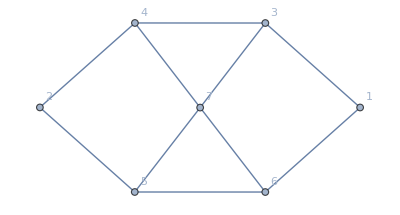

```mathematica
edges2graph[edgelist_]:=DeleteCases[Flatten[Table[Table[Block[{ilen=Length[Intersection[edgelist[[i]],edgelist[[j]]]]},Piecewise[{{i<->j, (ilen>0∧i≠j)}, {0, (ilen==0∨i==j)}}]],{i,1,j}],{j,1,Length[edgelist]}]],0]
Graph[edges2graph[{{{0,0},{1,0}},{{1,1},{0,1}},{{1,0},{1,1/2}},{{1,1/2},{1,1}},{{0,1},{0,1/2}},{{0,1/2},{0,0}},{{1,1/2},{0,1/2}}}],VertexLabels->"Name"]
```

```mathematica
RegionPlot[Polygon[{{0,0},{1,0},{1,1},{0,1}}]]
```

-Graphics-

```mathematica
RegionQ[RegionIntersection[Line[{{0,0},{1,1}}],Line[{{0,1},{1,0}}]]]
```

True

```mathematica
RegionQ[RegionIntersection[Line[{{1,0},{1,1}}],Line[{{0,0},{0,1}}]]]
```

True

```mathematica
lineinter[linepts1_,linepts2_]:=Block[{reginter=RegionIntersection[Line[linepts1],Line[linepts2]]},Piecewise[{{RegionCentroid[reginter], RegionMeasure[reginter]≠0}, {0, RegionMeasure[reginter]==0}}]]
lineinter[{{0,0},{1,1}},{{0,1},{1,0}}]
lineinter[{{1,0},{1,1}},{{0,0},{0,1}}]
lineinter[{{1,0},{1,2}},{{0,1},{2,1}}]
```

{1/2,1/2}

0

{1,1}

```mathematica
lineinterq[linepts1_,linepts2_]:=Quiet[Piecewise[{{(RegionMeasure[RegionIntersection[Line[linepts1],Line[linepts2]]]≠0), RegionQ[RegionIntersection[Line[linepts1],Line[linepts2]]]}, {False, ¬RegionQ[RegionIntersection[Line[linepts1],Line[linepts2]]]}}]]
lineinterq[{{0,0},{1,1}},{{0,1},{1,0}}]
lineinterq[{{1,0},{1,1}},{{0,0},{0,1}}]
```

True

False

```mathematica
lineinterq[Line[{{3/2,5/2},{5/2,3/2}}],Line[{{4,1},{1,2}}]]
```

False

```mathematica
RegionMeasure[Line[{{0,0},{1,1}}]]+RegionMeasure[Line[{{0,1},{1,0}}]]
RegionMeasure[RegionUnion[Line[{{0,0},{1,1}}],Line[{{0,1},{1,0}}]]]
```

2 √2

2 √2

```mathematica
RegionMeasure[Line[{{1,4},{4,5}}]]+RegionMeasure[Line[{{9/2,4},{4,5/2}}]]==3 √(5/2)
```

True

```mathematica
RegionMeasure[RegionUnion[Line[{{1,4},{4,5}}],Line[{{9/2,4},{4,5/2}}]]]
```

3 √(5/2)

```mathematica
RegionQ[RegionIntersection[Line[Line[{{1,4},{4,5}}]],Line[Line[{{9/2,4},{4,5/2}}]]]]
```

RegionIntersection::reg: Line[Line[{{1, 4}, {4, 5}}]] is not a correctly specified region.

False

```mathematica
lineinterq[Line[{{1,4},{4,5}}],Line[{{9/2,4},{4,5/2}}]]
```

RegionIntersection::reg: Line[Line[{{1, 4}, {4, 5}}]] is not a correctly specified region.

False

```mathematica
RegionBounds[RegionIntersection[Line[{{0,0},{1,1}}],Line[{{0,1},{1,0}}]]]
```

{{1/2,1/2},{1/2,1/2}}

```mathematica
RegionBounds[RegionIntersection[Line[{{1,0},{1,1}}],Line[{{0,0},{0,1}}]]]
```

{{∞,-∞},{∞,-∞}}

```mathematica
RegionCentroid[RegionIntersection[Line[{{1,1/2},{0,1/2}}],Line[{{1,0},{1,1}}]]]
```

{1,1/2}

```mathematica
RegionMeasure[RegionIntersection[Line[{{1,1/2},{0,1/2}}],Line[{{1,0},{1,1}}]]]
```

1

```mathematica
RegionMeasure[RegionIntersection[Line[{{1,0},{1,1}}],Line[{{0,0},{0,1}}]]]
```

0

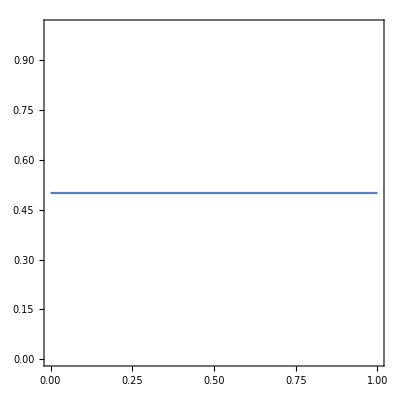

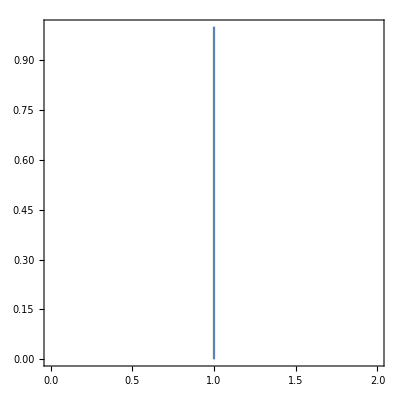

```mathematica
RegionPlot[Line[{{1,1/2},{0,1/2}}]]
RegionPlot[Line[{{1,0},{1,1}}]]
```